# YUAN ISP Laplace Transforms

## 3.

```mathematica
Integrate[2x E^(-s x),{x,0,∞}]
```

ConditionalExpression[2/s^2,Re[s]>0]

```mathematica
s LaplaceTransform[x^2,x,s]
```

2/s^2

```mathematica
test[f_,indvar_]:=LaplaceTransform[D[f,indvar],indvar,s]==(s LaplaceTransform[f,indvar,s]-f/.{indvar->0})//FullSimplify
```

```mathematica
test[t Cos[t],t]
```

True

```mathematica
test[f,t]
```

True

## 6.

```mathematica
Text@Grid[{{"Function","Transform"},{"n (any number)",LaplaceTransform[n,t,s]},{"e^ax",LaplaceTransform[E^(a x),x,s]},{Cos[a x],LaplaceTransform[Cos[a x],x,s]},{Sin[a x],LaplaceTransform[Sin[a x],x,s]},{x^n,LaplaceTransform[x^n,x,s]},
{n^x,LaplaceTransform[n^x,x,s]}},Frame->All,Spacings->{2,1}]
```

Function | Transform
n (any number) | n/s
e^ax | 1/(-a+s)
Cos[a x] | s/(a^2+s^2)
Sin[a x] | a/(a^2+s^2)
x^n | s^(-1-n) Gamma[1+n]
n^x | 1/(s-Log[n])

## 7.

```mathematica
given=1/2 E^(-Sqrt[2]t)(1+E^(2Sqrt[2]t));
```

```mathematica
y[t]/.DSolve[{y''[t]-2y[t]==0,y[0]==1,y'[0]==0},y[t],t][[1]]
given==%
```

1/2 ⅇ^(-√2 t) (1+ⅇ^(2 √2 t))

True

The DSolve output of the differnetial equation agrees with the given  expression.

This can be further affirmed using Mathematica’s built in expression, LaplaceTransform:

```mathematica
L=LaplaceTransform[y[t],t,s];
```

```mathematica
Evaluate@LaplaceTransform[y''[t]-2y[t],t,s]
```

```mathematica
L/.(Solve[LaplaceTransform[y''[t]-2y[t],t,s]==LaplaceTransform[0,t,s],L][[1]])/.{y[0]->1,y'[0]->0}
InverseLaplaceTransform[%,s,t]
given==%
```

s/(-2+s^2)

1/2 ⅇ^(-√2 t) (1+ⅇ^(2 √2 t))

True

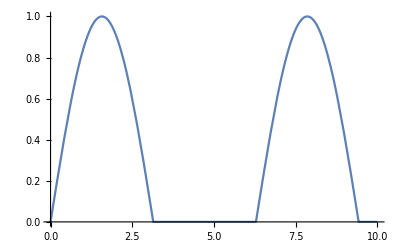

```mathematica
Plot[Sin[t]/2+Abs[Sin[t]]/2,{t,0,10}]
```

## Inversion Methods (Because I think it’s stupid to have to reference a grid or a database of known Laplace Transforms..)

Interestingly, the Inverse laplace can be evaluated by its integral form where L^-1[f(s)]==F(t)=1/(2Pi i)(∫^(α+i ∞))_(α-i∞)e^(s t)f(s)ds

Even crazier, this complex integral can be evaluated by using the cauchy residue theorem which turns out to be an extension of Stokes theorem in order to caclulate this line integral, along the Bromwich contour. Which actually makes sense bc it says the sum of all the residues of the individual points inside of the contour can be found through the path integral (what happens on the boundary). Again fundamental theorem of calc, truly Fundamental.

```mathematica
LaplaceTransform[Sin[x],x,s]
```

1/(1+s^2)

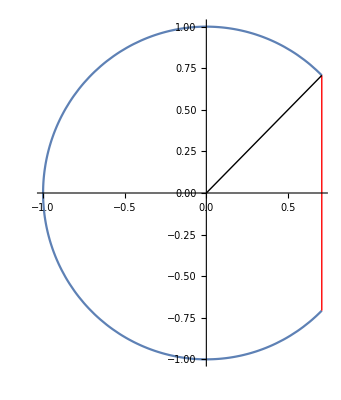

```mathematica
Show[ParametricPlot[{Cos[t],Sin[t]},{t,Pi/4,2Pi-Pi/4}],Graphics[{{Red,Line[{{Cos[Pi/4],Sin[Pi/4]},{Cos[Pi/4],-Sin[Pi/4]}}]},Line[{{0,0},{Cos[Pi/4],Sin[Pi/4]}}]}]]
```

THis is what the bromwich curve somewhat looks like where the red line is represneted as a line s=x+i y=α. Interes

Actually, this means that even at the places where along c1 the integral is equal to 0, along the complex path, the integral is equal to the sum of the residues of all the singular points inside c. Then one can also find that the ∫_C f(z)dz==2Pi i a_-1, where a_-1 is( the coefficient of 1/(z-a))of the laurent expansion.Whats then cool is that this is the exact format of our integral in order to find the inverse laplace. Therefore our a_-1 our residue is equal to 1/(2Pi)∫_C E^(s t)f(s)ds in our laplace equation. we can take the limit of R as it approaches infinity to account for the sum of all residues of all isolated singular points inside C

```mathematica
inverseLaplace[f_,indvar_]:=(poles=TransferFunctionPoles[TransferFunctionModel[{{f}},indvar]][[1,1]];
res=Table[Residue[f E^(indvar t),{indvar,i}],{i,poles}];
Total[res]//FullSimplify)
```

THIS IS SO COOL MY MIND IS BLOWN. Apparently residue is a number proportional to the contour plot of a fucntion enclosing one of its singularities. However, stokes allows us to account for all singularities

```mathematica
inverseLaplace[1/((s+1)(s-2)^2),s]
TrueQ[%==InverseLaplaceTransform[LaplaceTransform[%,t,s],s,t]//FullSimplify]
```

ⅇ^-t/9+2/9 ⅇ^(2 t) (-1+3 t)

True

Solving a diffeq

```mathematica
sysSolve[diffEq_,init_List,f_,indvar_]:=(lapTrans=LaplaceTransform[f,indvar,s]/.Solve[(LaplaceTransform[diffEq,indvar,s])/.init,LaplaceTransform[f,indvar,s]][[1]];
inverseLaplace[lapTrans,s])
```

```mathematica
sysSolve[y''''[t]+2y''[t]+y[t]==Sin[t],{y[0]->1,y'[0]->-2,y''[0]->3,y'''[0]->0},y[t],t]
```

3/8 ((8+5 t) Cos[t]-(21+(-16+t) t) Sin[t])

Here are some pretty cool numerical inverses that people have built (below) for simple Laplace transforms too!

```mathematica
Manipulate[
Module[{plt1,plt2,tbl,f,F},
F[p_]:=1/(p^2+1);
f[t_]:= Exp[σ t]/T (1/2 F[σ]+∑_(k=1)^100 (Re[F[σ+(k π I)/T]] Cos[(k π t)/T]-Im[F[σ+(k π I)/T]] Sin[(k π t)/T]));
tbl=Table[{t,f[t]},{t,0,50,0.5}];plt1=Plot[Sin[t],{t,0,50},Frame-> True,PlotStyle-> {Thick,ColorData[1,2]},FrameLabel-> {Style["x",Italic],Row[{"sin(",Style["x",Italic],")"}]}];plt2=ListPlot[tbl,Frame-> True,FrameLabel-> {Style["x",Italic],Row[{"sin(",Style["x",Italic],")"}]},Joined-> True,PlotMarkers-> Automatic,PlotStyle-> Thickness[0.005]];
Show[plt2,plt1,ImageSize-> {500,350}]],
{{T,50,"T"},20,100,1,Appearance->"Labeled"},
{{σ,0.2,"ο"},0.01,0.8,0.01,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Module[{plt1,plt2,F,t,fexact,finv,α,k},
α={1.283767675 10^1+I 1.666063445,
1.222613209 10^1+I 5.012718792,
1.09343031 10^1+I 8.40967312,
8.77643472+ I 1.19218539 10^1,
5.22545336+I 1.57295290 10^1};
k={-3.69020821 10^4+I 1.96990426 10^5,
6.12770252 10^4-I 9.54086255 10^4,
-2.89165629 10^4+ I 1.81691853 10^4,
4.65536114 10^3- I 1.90152864,
-1.18741401 10^2-I 1.41303691 10^2}; t=Table[i,{i,0.5,10,0.5}];
F[s_]:=1/(a2 s^2 + a1 s+a0);
fexact[t_]:=InverseLaplaceTransform[F[s],s,t];
plt1=Plot[fexact[t],{t,0,10},PlotStyle-> RGBColor[.48,.11,.56]];
finv=2/t ∑_(i=1)^5 Re[k[[i]] F[α[[i]]/t]];plt2=ListPlot[Transpose[{t,finv}],PlotStyle-> {PointSize[0.025],RGBColor[0,0,.49]},Frame-> True,FrameLabel-> {Style["t",Italic],Row[{Style["f",Italic],"(",Style["t",Italic],")"}]}] ;
Show[plt2,plt1,ImageSize-> {500,300},ImagePadding->{{50,10},{40,10}}]],
{{a0,1,"a_0"},-5,5,0.5,Appearance->"Labeled"},
{{a1,1,"a_1"},1,5,0.5,Appearance->"Labeled"},
{{a2,1,"a_2"},1,5,0.5,Appearance->"Labeled"}]
```